```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 121 Kb

{Utilities`CleanSlate`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[q]
q = { x1[t] , x2[t] , x3[t] }
```

{x1[t],x2[t],x3[t]}

```mathematica
Clear[eom]
eom = { 
m x1''[t] == k ( x2[t] - x1[t]  ) ,
M x2''[t] == k ( x1[t] - 2 x2[t] + x3[t] ) ,
m x3''[t] == - k ( x3[t] - x2[t] ) 
} ;
eom // TableForm
```

m x1''[t]==k (-x1[t]+x2[t])
M x2''[t]==k (x1[t]-2 x2[t]+x3[t])
m x3''[t]==-k (-x2[t]+x3[t])

```mathematica
Clear[parameters]
parameters = {
m-> 1 , 
M-> 2 , 
k-> 30 
};
parameters // TableForm
```

m→1
M→2
k→30

```mathematica
eom /. parameters  // Expand // TableForm
```

x1''[t]==-30 x1[t]+30 x2[t]
2 x2''[t]==30 x1[t]-60 x2[t]+30 x3[t]
x3''[t]==30 x2[t]-30 x3[t]

```mathematica
Clear[ics]
ics = { 
x1[0] == 0 ,
x1'[0] == 0.1 ,
x2[0] == 0 , 
x2'[0] == 0.1 ,
x3[0] == 0 ,
x3'[0] == -0.1
};
ics // TableForm
```

x1[0]==0
x1'[0]==0.1
x2[0]==0
x2'[0]==0.1
x3[0]==0
x3'[0]==-0.1

```mathematica
Clear[solution]
solution =
First[NDSolve[ Union[ eom /. parameters , ics ] , q , { t , 0, 10 } ]]
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t]}}

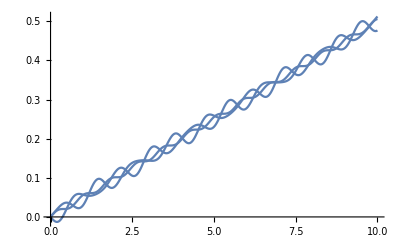

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

```mathematica
Clear[trial]
trial = { 
x1[t]-> A1 Cos[ ω t ] , 
x2[t]-> A2 Cos[ ω t ] ,
x3[t]-> A3 Cos[ ω t ] 
} ;
trial // TableForm
```

x1[t]→A1 Cos[t ω]
x2[t]→A2 Cos[t ω]
x3[t]→A3 Cos[t ω]

```mathematica
D[trial, t] // TableForm
```

x1'[t]→-A1 ω Sin[t ω]
x2'[t]→-A2 ω Sin[t ω]
x3'[t]→-A3 ω Sin[t ω]

```mathematica
D[D[trial, t], t] // TableForm
```

x1''[t]→-A1 ω^2 Cos[t ω]
x2''[t]→-A2 ω^2 Cos[t ω]
x3''[t]→-A3 ω^2 Cos[t ω]

```mathematica
eom /. trial /. D[D[trial, t], t] // Expand  // TableForm
```

-A1 m ω^2 Cos[t ω]==-A1 k Cos[t ω]+A2 k Cos[t ω]
-A2 M ω^2 Cos[t ω]==A1 k Cos[t ω]-2 A2 k Cos[t ω]+A3 k Cos[t ω]
-A3 m ω^2 Cos[t ω]==A2 k Cos[t ω]-A3 k Cos[t ω]

```mathematica
Clear[eqTrial]
eqTrial = eom /. trial /. D[D[trial, t], t] // Expand ;
eqTrial // TableForm
```

-A1 m ω^2 Cos[t ω]==-A1 k Cos[t ω]+A2 k Cos[t ω]
-A2 M ω^2 Cos[t ω]==A1 k Cos[t ω]-2 A2 k Cos[t ω]+A3 k Cos[t ω]
-A3 m ω^2 Cos[t ω]==A2 k Cos[t ω]-A3 k Cos[t ω]

```mathematica
Clear[eqTrial1]
eqTrial1 = 
Assuming[ Cos[ ω t] ≠ 0 , 
DivideSides[ eqTrial , Cos[ ω t ] ] ] // Expand  ;
eqTrial1 // TableForm
```

-A1 m ω^2==-A1 k+A2 k
-A2 M ω^2==A1 k-2 A2 k+A3 k
-A3 m ω^2==A2 k-A3 k

```mathematica
eqTrial[[1]]
eqTrial[[1,1]]
eqTrial[[1,2]]
```

-A1 m ω^2 Cos[t ω]==-A1 k Cos[t ω]+A2 k Cos[t ω]

-A1 m ω^2 Cos[t ω]

-A1 k Cos[t ω]+A2 k Cos[t ω]

```mathematica
Clear[A]
A = { A1 , A2 , A3 }
```

{A1,A2,A3}

```mathematica
Coefficient[ eqTrial1[[1,1]] , A ] - Coefficient[ eqTrial1[[1,2]] , A ]
Coefficient[ eqTrial1[[2,1]] , A ] - Coefficient[ eqTrial1[[2,2]] , A ]
Coefficient[ eqTrial1[[3,1]] , A ] - Coefficient[ eqTrial1[[3,2]] , A ]
```

{k-m ω^2,-k,0}

{-k,2 k-M ω^2,-k}

{0,-k,k-m ω^2}

```mathematica
Clear[secular]
secular = 
Table[ 
Coefficient[ eqTrial1[[i,1]] , A ] - Coefficient[ eqTrial1[[i,2]] , A ] , { i , 1 , 3 } ] ;
secular // MatrixForm
```

(k-m ω^2 | -k | 0
-k | 2 k-M ω^2 | -k
0 | -k | k-m ω^2)

```mathematica
Solve[ Det[ secular ]  == 0  , ω ]
```

{{ω→0},{ω→0},{ω→-(√k)/(√m)},{ω→(√k)/(√m)},{ω→-(√k √(2 m+M))/(√m √M)},{ω→(√k √(2 m+M))/(√m √M)}}

```mathematica
Solve[ Det[ secular ]  == 0  , ω ] [[2]] /. ω-> ω3
Solve[ Det[ secular ]  == 0  , ω ] [[4]] /. ω-> ω1
Solve[ Det[ secular ]  == 0  , ω ] [[6]] /. ω-> ω2
```

{ω3→0}

{ω1→(√k)/(√m)}

{ω2→(√k √(2 m+M))/(√m √M)}